```mathematica
css zebrafinch model;
ns is number of stressed juveniles;
nh is number of health juveniles;
NNA is number of adapted adults;
NNn is number of nonadapted adults;

ba: benefit of adaptive behavior on fecundity;
bn: benefit of non-adaptive behavior on fecundity;
pa: probability an adapted adult produces stressed offspring;
pn: probability a nonadapted adult produces stressed offspring;
vs: vitality (opposite of mortality rate) of a stresed juvenille;
vh: vitality (opposite of mortality rate) of a healthy juvenille;
vI: mortality cost of ndividual learning;
lsO : frequency of oblique learners who were stressed juveniles;
lhO : frequency of oblique learners who were healthy juveniles;


Recursions;
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs((1-lsV) vI z +lsV qV ) + nh vh((1-lhV) vI z +lhV qV );
NNn :=ns vs((1-lsO) vI (1-z)+lsO(1- qO) ) + nh vh((1-lhO) vI (1-z)+lhO(1- qO) );
qO := (1-u)(ba Na/(ba Na +bn Nn));
```

```mathematica
Transition Matrix;
(*leave Q in matrix below different than one up above recursions*)
AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs((1-lsV) vI z +lsV Qh), vh((1-lhV) vI z +lhV Qh ), 0, 0}, {vs((1-lsV) vI (1-z)+lsV(1- Qh) ), vh((1-lhV) vI (1-z)+lhV(1- Qh) ), 0, 0}})
```

```mathematica
NN = FullSimplify[NNn + NNa];
```

```mathematica
FFa=FullSimplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
FFn=FullSimplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
solve Q-hat for common strategy;
Fasols=Solve[FFa==Fa,Fa];
```

```mathematica
PSTYLE={Directive[RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862]],Directive[RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961]],Directive[RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824]],Directive[RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961]],Directive[RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253]],Directive[RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],Dashed],Directive[RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],Dashed],Directive[RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],Dashed],Directive[RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],Dashed],Directive[RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],Dashed]};
ulist={0.01,0.05,0.1, 0.25, 0.5 };
blist={1.5,2,3,5};
llsVstart=0;
llhVstart=-4 ;
imax=1000;
lhVtab=lsVtab=llhVtab=llsVtab=Table[0,{i,imax-1}];
delta=16;
llsVtab[[1]]=llsVstart;
llhVtab[[1]]=llhVstart;
```

Part::partd: Part specification {{{1.,0.0179862},{2.,0.0146308},{3.,0.00396508-0.0142493 ⅈ},{4.,-0.00551636-0.0074995 ⅈ},{5.,-0.00416902-0.00266516 ⅈ},{6.,-0.00279699-0.00126133 ⅈ},{7.,-0.00199491-0.000719765 ⅈ},{8.,-0.00149992-0.000458258 ⅈ},«36»,{45.,-0.000047975-2.59937×10^-6 ⅈ},{46.,-0.000045944-2.43667×10^-6 ⅈ},{47.,-0.0000440397-2.2873×10^-6 ⅈ},{48.,-0.0000422518-2.14993×10^-6 ⅈ},{49.,-0.000040571-2.02337×10^-6 ⅈ},{50.,-0.0000389888-1.90658×10^-6 ⅈ},«949»},{«1»},«6»,{«1»},{{1.,0.5},«49»,«949»}}⟦«1»⟧ is longer than depth of object.

Callout::copos: {Bottom {0.984375,0}[{0.508993,43/94+1.05 {{«999»},{«999»},{«999»},{«999»},{«999»},{«999»},{«999»},{«999»},{«999»},{«999»}}⟦All,All,2,2⟧}],Automatic} is not a valid position for the placement of callouts.

Callout::copos: {Bottom {0.984375,0}[{0.508993,95/282+1.05 {{«999»},{«999»},{«999»},{«999»},{«999»},{«999»},{«999»},{«999»},{«999»},{«999»}}⟦All,All,2,2⟧}],Automatic} is not a valid position for the placement of callouts.

Callout::copos: {Bottom {0.984375,0}[{0.508993,67/282+1.05 {{«999»},{«999»},{«999»},{«999»},{«999»},{«999»},{«999»},{«999»},{«999»},{«999»}}⟦All,All,2,2⟧}],Automatic} is not a valid position for the placement of callouts.

General::stop: Further output of Callout::copos will be suppressed during this calculation.

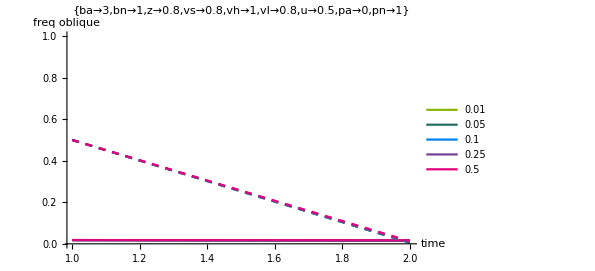
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
For[j=1,j≤Length[blist],j++,{
For[h=1,h≤Length[ulist],h++,{
subs = {ba->blist[[j]],bn->1,z->0.8,vs->.8,vh->1,vI->0.8 ,u->ulist[[h]] , pa -> 0, pn-> 1};
test = {lsV->0  ,lsI-> 0.8,lhV-> 0.8,lhI-> 0.2};
QHAT[LHV_,LSV_] :=Simplify[Fasols[[1,1,2]]/.{lhO->LHO,lhI -> LHI, lsO -> LSO, lsI-> LSI} /.subs];
(*isolate dominant eigenvalue*)
AA2=AA/.subs;
LL=Eigenvalues[AA2];
(*isolate Dominant eigenvalue, substitute in q-hat *)
Lambda1= Simplify[LL[[2]]/.Qh->  QHAT[LHV,LSV] ];
            softmaxsubs ={lsV -> Exp[llsV]/(1 +  Exp[llsV]) , lhV -> Exp[llhV]/(1 +  Exp[llhV]) ,LSV -> Exp[LLSV]/(1 +  Exp[LLSV]) , LHV -> Exp[LLHV]/(1 +  Exp[LLHV]) };
	  Lambda2[ llsV_, llhV_,LLHV_,LLSV_]:=Lambda1 /.softmaxsubs;

(*take partial derivatives to calculate gradient, substitute mutant for common type*)
DllsV=D[Lambda2[llsV, llhV,LLHV,LLSV],llsV]/. {LLHV -> llhV,LLSV-> llsV};
DllhV=D[Lambda2[llsV, llhV,LLHV,LLSV],llhV]/. {LLHV -> llhV,LLSV-> llsV};
(*try and graph*)

llsVtab[[1]]=llsVstart;
llhVtab[[1]]=llhVstart;


For[i=2,i<imax,i++,{
llsVtab[[i]]=llsVtab[[i-1]]  + delta DllsV/.subs/.{llsV->llsVtab[[i-1]],llhV->llhVtab[[i-1]]};
llhVtab[[i]]=llhVtab[[i-1]]  + delta DllhV/.subs/.{llsV->llsVtab[[i-1]],llhV->llhVtab[[i-1]]};
}]; 

lsVtab =Exp[llsVtab]/(1+Exp[llsVtab]);
lhVtab =Exp[llhVtab]/(1+Exp[llhVtab]);

lsVtab1=If[h==1,lsVtab,lsVtab1];
lsVtab2=If[h==2,lsVtab,lsVtab2];
lsVtab3=If[h==3,lsVtab,lsVtab3];
lsVtab4=If[h==4,lsVtab,lsVtab4];
lsVtab5=If[h==5,lsVtab,lsVtab5];
lhVtab1=If[h==1,lhVtab,lhVtab1];
lhVtab2=If[h==2,lhVtab,lhVtab2];
lhVtab3=If[h==3,lhVtab,lhVtab3];
lhVtab4=If[h==4,lhVtab,lhVtab4];
lhVtab5=If[h==5,lhVtab,lhVtab5];
}];

plotcode=ListLinePlot[{lhVtab1,lhVtab2,lhVtab3,lhVtab4,lhVtab5, lsVtab1,lsVtab2,lsVtab3,lsVtab4,lsVtab5},PlotLabels->ulist,PlotRange->{All,{0,1}},PlotStyle->PSTYLE,AxesLabel->{time, freq vertical},PlotLegends->{Placed[PointLegend[ulist],Bottom],Placed[LineLegend[{Normal,Dashed},{"healthy juv","stressed juv"}],Top]},PlotLabel->subs, ImageSize->440];

p1 = If[j≠1,p1,plotcode];
       p2 = If[j≠2,p2,plotcode];
       p3 = If[j≠3,p3,plotcode];
       p4 = If[j≠4,p4,plotcode];

}];              
Grid[{{p1,p2,p3,p4}} ]
```

```mathematica
Eigenvalues[AA2]/.test /.Qh->0.2
```

{-1.50017,1.50017,0.-0.826143 ⅈ,0.+0.826143 ⅈ}

```mathematica
Eigenvalues[AA2]
```

{Root[-0.512 lhO+0.512 lsO+0.64 lhO Qh-0.64 lsO Qh+(-0.6656+0.64 lhO-0.1344 lsO-1. lhO Qh+0.16 lsO Qh) #1^2+0.2 #1^4&,1],Root[-0.512 lhO+0.512 lsO+0.64 lhO Qh-0.64 lsO Qh+(-0.6656+0.64 lhO-0.1344 lsO-1. lhO Qh+0.16 lsO Qh) #1^2+0.2 #1^4&,2],Root[-0.512 lhO+0.512 lsO+0.64 lhO Qh-0.64 lsO Qh+(-0.6656+0.64 lhO-0.1344 lsO-1. lhO Qh+0.16 lsO Qh) #1^2+0.2 #1^4&,3],Root[-0.512 lhO+0.512 lsO+0.64 lhO Qh-0.64 lsO Qh+(-0.6656+0.64 lhO-0.1344 lsO-1. lhO Qh+0.16 lsO Qh) #1^2+0.2 #1^4&,4]}